error= 8.40833×10^-3

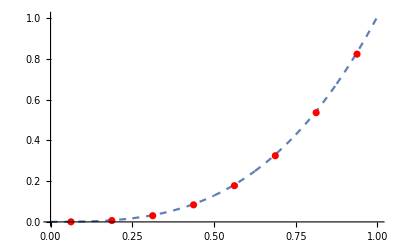

```mathematica
Remove["Global`*"];
H[XX_]:=Module[{xx=XX},
Subscript[h, 1][xx_]=Piecewise[{{1,0≤ xx<1}}];
For[j=0,j≤ J,j++,
For[k=0,k≤ 2^j-1,k++,
Subscript[h, 2^j+k+1][xx_]=Piecewise[{{1,k/2^j≤ xx<(k+0.5)/2^j},{-1,(k+0.5)/2^j≤ xx≤ (k+1)/2^j}},0];
];
];
];
(*****************************************)
K[x_,t_]=Cos[x-t];
g[t_]=6(1-Cos[t]);
yReal[t_]=t^3;
a=0;
(*****************************************)
M=4;J=2;
AA=Table[Subscript[aa, i],{i,2M}];
KK[x_,t_]=N[D[K[x,t],x]/K[x,x],20];
gp1[x_]=N[D[g[x],x]/K[x,x],20];
For[l=1,l≤ 2M,l++,Subscript[𝓍, l]=(l-0.5)/(2 M)];
H[x];
ℐ=ParallelTable[∫_a^Subscript[𝓍, l] KK[Subscript[𝓍, l],t]Subscript[h, i][t]ⅆt,{i,2M},{l,2M}];
Ans=ParallelTable[∑_(i=1)^(2M) Subscript[aa, i](Subscript[h, i][Subscript[𝓍, l]]+ℐ⟦i,l⟧)-gp1[Subscript[𝓍, l]],{l,1,2M}];
AA=Flatten[AA/.Solve[Ans==0,AA]];
w[t_]=Simplify[∑_(i=1)^(2M) AA⟦i⟧Subscript[h, i][t]];
Subscript[yt, J][t_]=∫∫w[t]ⅆtⅆt;
error=Table[Subscript[yt, J][Subscript[𝓍, l]]-yReal[Subscript[𝓍, l]],{l,1,2M}];
Subscript[MAE, J]=Max[error];
Print["error= ",ScientificForm[Subscript[MAE, J]]]
Show[Plot[Subscript[yt, J][t],{t,0,1},PlotStyle->{Dashed}],ListPlot[Table[{Subscript[𝓍, l],yReal[Subscript[𝓍, l]]},{l,1,2M}],PlotStyle->{Red}]]
```